```mathematica
f[x_]:= x^4-2 x^3-2 x^2
```

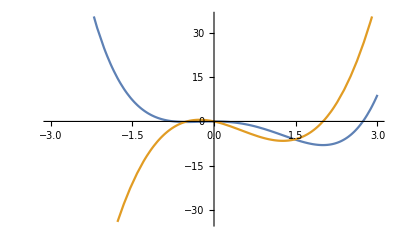

```mathematica
Plot[{f[x],f'[x]}, {x, -3,3}]
```

```mathematica
Solve[{f'[x1]==f'[x2], x1≤ -1/2, x2<2}]
```

{{x2→ConditionalExpression[x1,1/6 (3-2 √21)<x1<-1/2||x1<1/6 (3-2 √21)]},{x2→ConditionalExpression[1/4 (3-2 x1)-1/4 √(25+12 x1-12 x1^2),1/6 (3-2 √21)<x1<-1/2]},{x2→ConditionalExpression[1/4 (3-2 x1)+1/4 √(25+12 x1-12 x1^2),1/6 (3-2 √21)<x1<-1/2]},{x1→-1/2,x2→-1/2},{x1→-1/2,x2→0},{x1→1/6 (3-2 √21),x2→1/6 (3-2 √21)},{x1→1/6 (3-2 √21),x2→-1/4 √(25+2 (3-2 √21)-1/3 (3-2 √21)^2)+1/4 (3+1/3 (-3+2 √21))}}